```mathematica
x1data = {-0.5, -0.42, -0.34, -0.26, -0.18, -0.1, -0.02, 0.06, 0.14, 0.22, 0.3, 0.38, 0.46, 0.54, 0.62, 0.7, 0.78, 0.86, 0.94, 1.02, 1.1, 1.18, 1.26, 1.34, 1.42};
y1data={0.535916, 0.485126, 0.437118, 0.371678, 0.301733, 0.207338, 0.073557, 0.155576, 0.283913, 0.390199, 0.497748, 0.592501, 0.69812, 0.789936, 0.898493, 0.990582, 1.10445, 1.19854, 1.31926, 1.4165, 1.54526, 1.64652,1.78436,1.89036, 2.03825};
data={};
For[i=1, i<26, i++,
data=Append[data,{x1data[[i]],y1data[[i]]}];
];
MatrixForm[data]
a = First[x1data]
b= Last[x1data]
```

(-0.5 | 0.535916
-0.42 | 0.485126
-0.34 | 0.437118
-0.26 | 0.371678
-0.18 | 0.301733
-0.1 | 0.207338
-0.02 | 0.073557
0.06 | 0.155576
0.14 | 0.283913
0.22 | 0.390199
0.3 | 0.497748
0.38 | 0.592501
0.46 | 0.69812
0.54 | 0.789936
0.62 | 0.898493
0.7 | 0.990582
0.78 | 1.10445
0.86 | 1.19854
0.94 | 1.31926
1.02 | 1.4165
1.1 | 1.54526
1.18 | 1.64652
1.26 | 1.78436
1.34 | 1.89036
1.42 | 2.03825)

-0.5

1.42

```mathematica
inpln:=InterpolatingPolynomial[data,x]
Collect[inpln,x]
```

0.066281+0.250268 x+29.8797 x^2-82.6739 x^3-1884.84 x^4+10481.2 x^5+40857.6 x^6-412375. x^7+288607. x^8+5.65948×10^6 x^9-1.71857×10^7 x^10-1.30425×10^7 x^11+1.54147×10^8 x^12-2.44453×10^8 x^13-2.31832×10^8 x^14+1.35659×10^9 x^15-1.79464×10^9 x^16-9.13108×10^7 x^17+3.61491×10^9 x^18-5.88224×10^9 x^19+5.23252×10^9 x^20-2.93323×10^9 x^21+1.03791×10^9 x^22-2.13205×10^8 x^23+1.94734×10^7 x^24

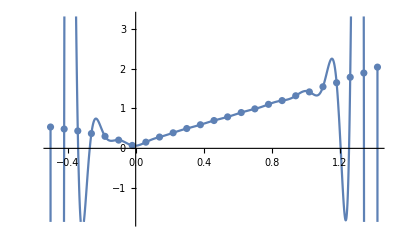

```mathematica
gr1:=Plot[inpln,{x,-0.5,1.42}];
gr2:=ListPlot[data];
Show[{gr1,gr2}]
```

```mathematica
data1={};
For[i=1, i<26, i+=2,
data1=Append[data1,{x1data[[i]],y1data[[i]]}];
];
MatrixForm[data1]
```

(-0.5 | 0.535916
-0.34 | 0.437118
-0.18 | 0.301733
-0.02 | 0.073557
0.14 | 0.283913
0.3 | 0.497748
0.46 | 0.69812
0.62 | 0.898493
0.78 | 1.10445
0.94 | 1.31926
1.1 | 1.54526
1.26 | 1.78436
1.42 | 2.03825)

```mathematica
inpln1:=InterpolatingPolynomial[data1,x]
Collect[inpln1,x]
```

0.0883836+0.900074 x+7.29475 x^2-31.9226 x^3+15.109 x^4+230.893 x^5-590.834 x^6+208.357 x^7+1283.89 x^8-2456.59 x^9+2017.52 x^10-815.908 x^11+132.599 x^12

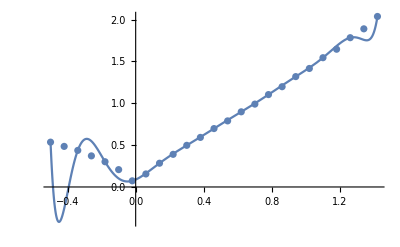

```mathematica
gr2:=ListPlot[data];
gr3:=Plot[inpln1,{x,-0.5,1.42}];
Show[{gr3,gr2}]
```

```mathematica
data2={};
For[i=1, i<26, i+=3,
data2=Append[data2,{x1data[[i]],y1data[[i]]}];
];
MatrixForm[data2]
```

(-0.5 | 0.535916
-0.26 | 0.371678
-0.02 | 0.073557
0.22 | 0.390199
0.46 | 0.69812
0.7 | 0.990582
0.94 | 1.31926
1.18 | 1.64652
1.42 | 2.03825)

```mathematica
inpln2:=InterpolatingPolynomial[data2,x]
Collect[inpln2,x]
```

0.08849+0.847463 x+4.78533 x^2-12.7153 x^3+3.11932 x^4+32.7907 x^5-52.0479 x^6+31.3522 x^7-6.82225 x^8

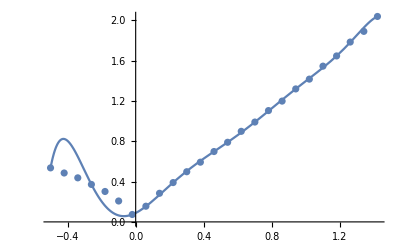

```mathematica
gr2:=ListPlot[data];
gr4:=Plot[inpln2,{x,-0.5,1.42}];
Show[{gr4,gr2}]
```

```mathematica
data3={};
For[i=1, i<26, i+=5,
data3=Append[data3,{x1data[[i]],y1data[[i]]}];
];
MatrixForm[data3]
```

(-0.5 | 0.535916
-0.1 | 0.207338
0.3 | 0.497748
0.7 | 0.990582
1.1 | 1.54526)

```mathematica
inpln3:=InterpolatingPolynomial[data3,x]
Collect[inpln3,x]
```

0.242899+0.51432 x+1.45617 x^2-1.26448 x^3+0.449193 x^4

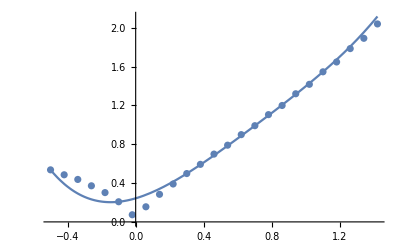

```mathematica
gr2:=ListPlot[data];
gr5:=Plot[inpln3,{x,-0.5,1.42}];
Show[{gr5,gr2}]
```

InterpolatingFunction[…]

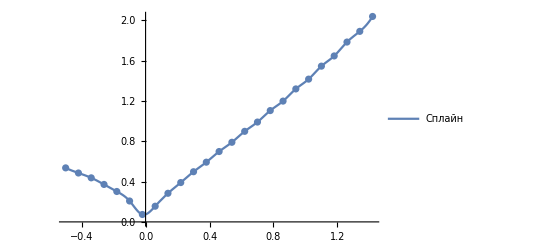

```mathematica
splain1=Interpolation[data,Method->"Spline"]
gr6 = Plot[{splain1[x]},{x,-0.5, 1.42},PlotLegends->{"Сплайн"}];
gr7=ListPlot[data];
Show[{gr6,gr7}]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

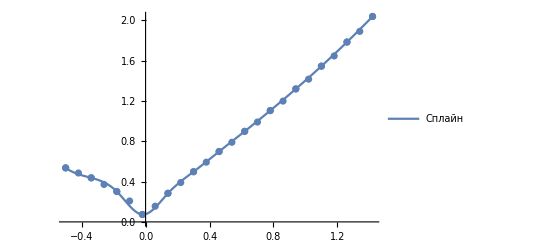

```mathematica
splain1=Interpolation[data,Method->"Spline"]
splain2=Interpolation[data1,Method->"Spline"]
gr7 = Plot[{splain2[x]},{x,-0.5, 1.42},PlotLegends->{"Сплайн"}];
gr2:=ListPlot[data];
gr8=ListPlot[data1];
Show[{gr2,gr7,gr8}]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

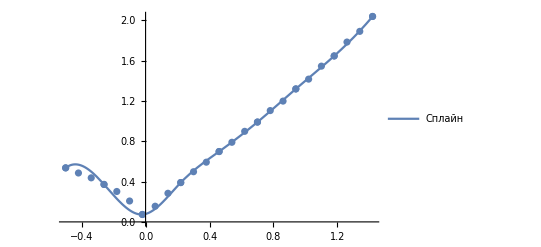

```mathematica
splain3=Interpolation[data,Method->"Spline"]
splain4=Interpolation[data2,Method->"Spline"]
gr9 = Plot[{splain4[x]},{x,-0.5, 1.42},PlotLegends->{"Сплайн"}];
gr2:=ListPlot[data];
gr10=ListPlot[data2];
Show[{gr2,gr9,gr10}]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

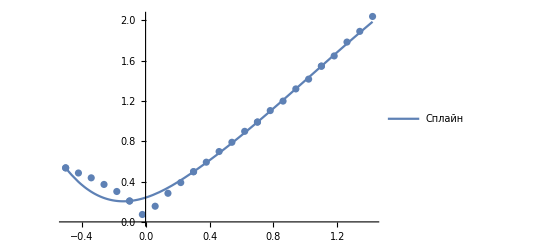

```mathematica
splain5=Interpolation[data,Method->"Spline"]
splain6=Interpolation[data3,Method->"Spline"]
gr11= Plot[{splain6[x]},{x,-0.5, 1.42},PlotLegends->{"Сплайн"}];
gr2:=ListPlot[data];
gr12=ListPlot[data3];
Show[{gr2,gr11,gr12}]
```

```mathematica
gr30[x_]=Fit[data,{1,x},x]
app[x_]=Fit[data,{1,x,x^2},x] 
app1[x_]=Fit[data,{1,x,x^2,x^3},x] 
app2[x_]=Fit[data,{1,x,x^2,x^3,x^4},x]
Sgrr1:=Plot[{gr30[x]},{x,-0.5,1.42},AspectRatio->Full,ImageSize->Large]
Sgrr2:=Plot[{app[x]},{x,-0.5,1.42},AspectRatio->Full,ImageSize->Large,PlotStyle->Yellow]
Sgrr3:=Plot[{app1[x]},{x,-0.5,1.42},AspectRatio->Full,ImageSize->Large, PlotStyle->Gray]
Sgrr4:=Plot[{app2[x]},{x,-0.5,1.42},AspectRatio->Full,ImageSize->Large,PlotStyle->Orange]
gr2:=ListPlot[data];
```

0.443208+0.919377 x

0.358353+0.275264 x+0.700123 x^2

0.250189+0.252709 x+1.54043 x^2-0.608918 x^3

0.235355+0.367251 x+1.66214 x^2-1.14416 x^3+0.290891 x^4

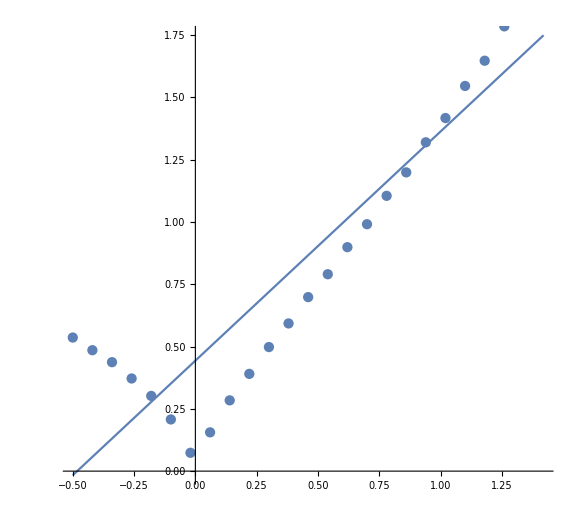

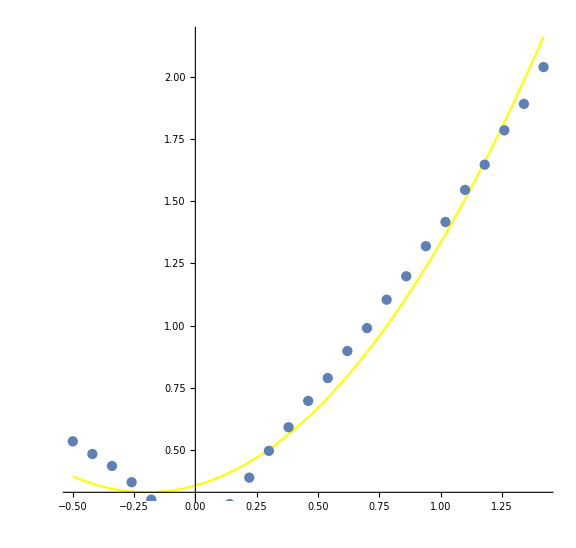

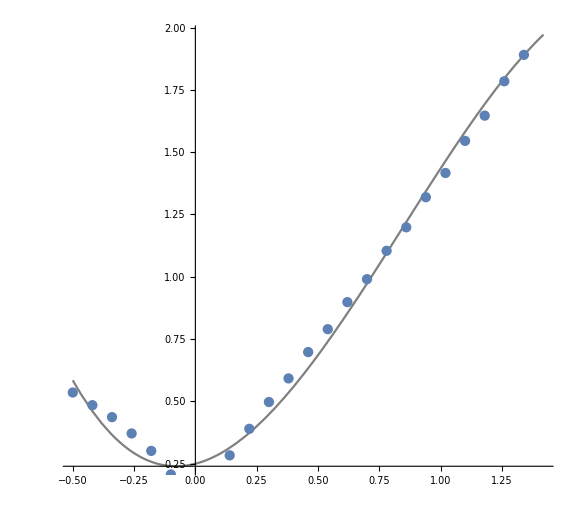

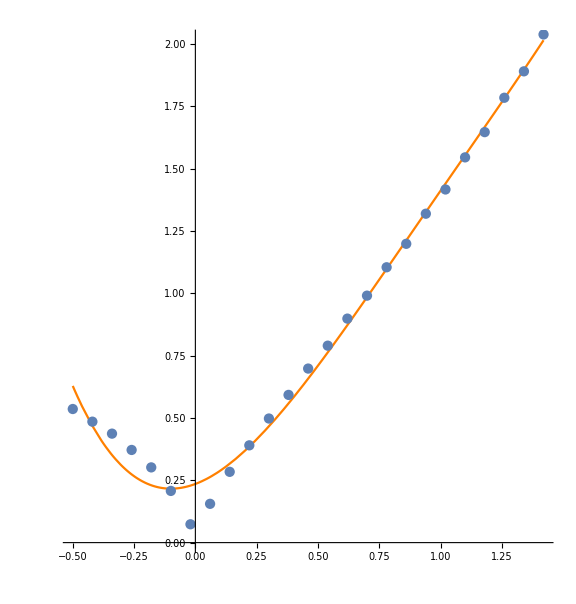

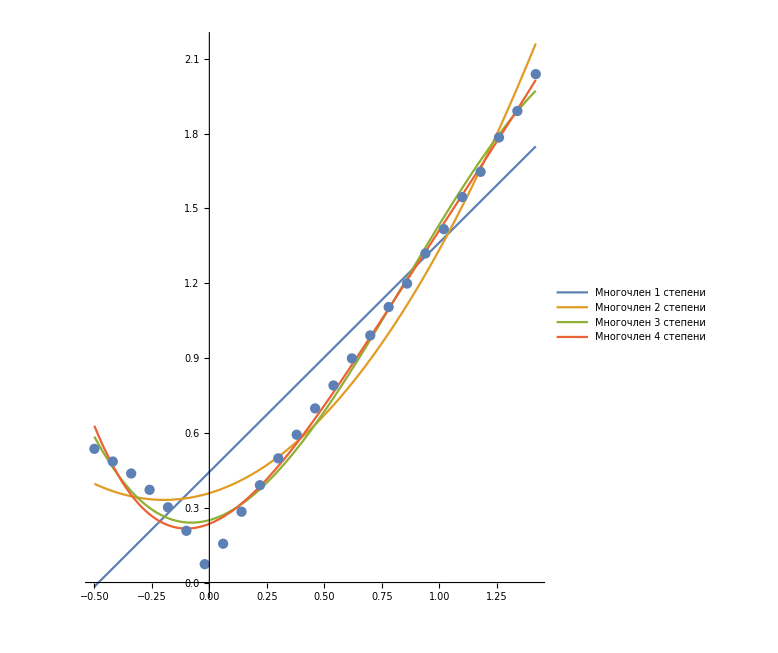

```mathematica
Show[Sgrr1,gr2]


Show[Sgrr2,gr2]

Show[Sgrr3,gr2]

Show[Sgrr4,gr2]
Show[Plot[{gr30[x],app[x],app1[x],app2[x]},{x,-0.5,1.42},PlotLegends->{"Многочлен 1 степени","Многочлен 2 степени","Многочлен 3 степени", "Многочлен 4 степени"}, AspectRatio->Full,ImageSize->Large],gr2]
```

```mathematica
For[i=1,i≤25,i++,
SumData[i]=N[gr30[x1data[[i]]]];];
sum=∑_(i=1)^25 (SumData[i]-y1data[[i]])^2
```

1.37428

```mathematica
For[i=1,i≤25,i++,
SumData[i]=N[app[x1data[[i]]]];];
sum=∑_(i=1)^25 (SumData[i]-y1data[[i]])^2
```

0.293715

```mathematica
For[i=1,i≤25,i++,
SumData[i]=N[app1[x1data[[i]]]];];
sum=∑_(i=1)^25 (SumData[i]-y1data[[i]])^2
```

0.0865592

```mathematica
For[i=1,i≤25,i++,
SumData[i]=N[app2[x1data[[i]]]];];
sum=∑_(i=1)^25 (SumData[i]-y1data[[i]])^2
```

0.07486

```mathematica
data={};
i = 1;
While[i<=Length[x1data],
data=Append[data,{x1data[[i]],y1data[[i]]}];
i=i+2;
];
step=(b-a)/(Length[x1data]-1);

(*Берем полином 12 степени
Встроеная функция*)
intp:=InterpolatingPolynomial[data,x];
Collect[intp,x]
sumIntegral = NIntegrate[intp,{x,a,b}];
Print["Интеграл с помощью встроенной функции (полином 12 степени): ",sumIntegral];

  (*Левые прямоугольники*)
	sumRec1=0;
For[i=1,i<Length[y1data],i++,
sumRec1=sumRec1+step*y1data[[i]];
];

(*Правые прямоугольники*)
sumRec2 =0;
For[i=2,i<Length[y1data]+1,i++,
sumRec2=sumRec2+step*y1data[[i]];
];

(*Метод Трапеций*)
sumTrap=First[y1data]+Last[y1data];
For[i=2,i<Length[y1data],i++,
sumTrap=sumTrap+2*y1data[[i]];
];

Print["Правые прямоугольники: ",sumRec1];
(*Print["Погрешность ",Abs[sumIntegral-sumRec1]];*)
Print["Левые прямоугольники: ",sumRec2];
(*Print["Погрешность ",Abs[sumIntegral-sumRec2]];*)
Print["Метод трапеции: ", step/2*sumTrap];
(*Print["Погрешность ",Abs[sumIntegral-(step/2*sumTrap)]];*)
Print["Метод Симпсона: ",step/3*(First[y1data]+4*∑_(i=1)^12 y1data[[2*i]]+2*∑_(i=2)^12 (y1data[[2*i-1]])+Last[y1data])];
```

0.0883836+0.900074 x+7.29475 x^2-31.9226 x^3+15.109 x^4+230.893 x^5-590.834 x^6+208.357 x^7+1283.89 x^8-2456.59 x^9+2017.52 x^10-815.908 x^11+132.599 x^12

Интеграл с помощью встроенной функции (полином 12 степени): 1.54264

Правые прямоугольники: 1.56918

Левые прямоугольники: 1.68937

Метод трапеции: 1.62928

Метод Симпсона: 1.62671